```mathematica
arena=<|
"DiskRadius"->0.6,
"ConeSemiAngle"->π/8,
"zRange"->{0,8}
|>;

d=arena["DiskRadius"]/Sin[arena["ConeSemiAngle"]];
initialDisks=<|1-><|"ID"->1,"Disk"->Disk[{0,d},arena["DiskRadius"]]
,"Polar"-><|"r"->d,"θ"->π/2|>
,"Supporters"->Missing[]
|>|>;
initialDisks=addDisk[arena,initialDisks,initialDisks[1],left[1]];
initialDisks=addDisk[arena,initialDisks,initialDisks[1],right[1]];
```

```mathematica
addDisk[arena_,disks_,disk_,ID_] := Append[disks,ID->disk];
addLRDisk[arena_,disks_,left[ID_]] := Append[disks,left[ID]->leftShift[arena,Lookup[disks,ID]]];
addLRDisk[arena_,disks_,right[ID_]] := Append[disks,right[ID]->rightShift[arena,Lookup[disks,ID]]]
```

```mathematica
leftQ[n_] := Head[n]===left;
rightQ[n_] := Head[n]===right;
shiftNumberRight[left[n_]] :=n;
shiftNumberRight[n_] :=right[n];

shiftNumberLeft[right[n_]] :=n;
shiftNumberLeft[n_] := left[n];

leftShift[arena_,xy_List] := RotationTransform[2 arena["ConeSemiAngle"]][xy];
rightShift[arena_,xy_List] := RotationTransform[-2 arena["ConeSemiAngle"]][xy];

leftShift[arena_,Disk[xy_,r_]] := Disk[leftShift[arena,xy],r];
rightShift[arena_,Disk[xy_,r_]] := Disk[rightShift[arena,xy],r];

leftShift[arena_,data_Association] := <|
"ID"->shiftNumberLeft[data["ID"]]
,"Disk"->leftShift[arena,data["Disk"]]
,"Polar"->leftPolar[arena,data["Polar"]]
,"Supporters"->shiftNumberLeft/@data["Supporters"]
|>;
rightShift[arena_,data_Association] := <|
"ID"->shiftNumberRight[data["ID"]],
"Disk"->rightShift[arena,data["Disk"]]
,"Polar"->rightPolar[arena,data["Polar"]]
,"Supporters"->shiftNumberRight/@data["Supporters"]
|>;
leftPolar[arena_,polar_Association] := Append[polar,"θ"->polar["θ"]+2 arena["ConeSemiAngle"]]
rightPolar[arena_,polar_Association] := Append[polar,"θ"->polar["θ"]-2 arena["ConeSemiAngle"]]
```

```mathematica
testRun[n_] := Module[{},
runDisks=initialDisks;
runChain={left[1],1,right[1]};
run=<|"Arena"->arena,"Disks"->runDisks,"Chain"->runChain|>;
run=Nest[addLowest,run,n];

displayRun[run]
]
```

```mathematica
addLowest[run_] := Module[{res,ixPairs,ID,ids,diskData,disks},
res=run;
ID=nextID[res];
diskData=lowestTangentDiskFromPairs[res,ID];
res["Disks"]= addDisk[res["Arena"],res["Disks"],diskData,ID];
res["Chain"]= updateChain[res,diskData];
ids=Complement[res["Chain"],Keys[res["Disks"]]];
res["Disks"]=Fold[addLRDisk[res["Arena"],#1,#2]&,res["Disks"],ids];
(*res["Graph"]=updateGraph[res,ID];
*)res
];
```

```mathematica
lowestTangentDiskFromPairs[run_,ID_]:= 
Module[{choices,arena,chainDisks,ixPairs,lowest},
arena=run["Arena"];
chainDisks=KeyTake[run["Disks"],run["Chain"]];
ixPairs=Subsets[run["Chain"],{2}];

choices=findTangentDisks[arena,chainDisks,ixPairs];
choices=Select[choices,!MissingQ[#Disk]&];
choices=Map[Append[#,"Polar"->disk2Polar[#Disk]]&,choices];
choices=pruneTangentDisks[arena,chainDisks,choices];
choices=SortBy[choices,#["Polar"]["r"]&];

lowest=First[choices];
lowest=Prepend[lowest,"ID"->ID];

If[lowest["InCone"]=="Left",
lowest=rightShift[arena,lowest]
];
If[lowest["InCone"]=="Right",
lowest=leftShift[arena,lowest]
];
lowest["ID"]=ID;
lowest
]
```

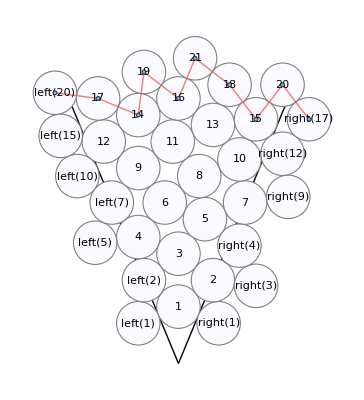

```mathematica
testRun[20]
```

```mathematica
findPairs[run_] := Module[{res=run,chainDisks,ixPairs},
chainDisks=res["Chain"];
ixPairs=Subsets[chainDisks,{2}];
ixPairs
];

nextID[run_] := Module[{ID,ids},
ids=Map[#["ID"]&,run["Disks"]];
ids=Max[Select[ids,NumberQ]];
ID=Max[ids]+1;
ID
];
```

```mathematica
updateChain[run_,disk_] := Module[{ID,supporters,chainGraph,chainNumbers,from,to,outSplice,debug},
ID=disk["ID"];
debug=(ID===0);
dp[x_] :=If[debug,(Print[x];x),x];


supporters=disk["Supporters"];
chainNumbers=run["Chain"];
If[debug,Print["Adding ", ID->supporters, "\n into ", chainNumbers]];
{from,to}=dp@Map[fom@fom@Position[chainNumbers,#,1]&,supporters];
If[from>to,supporters=Reverse[supporters]];
If[leftQ[supporters[[1]]],chainNumbers[[1]]=supporters[[1]]];
If[rightQ[supporters[[2]]],chainNumbers[[-1]]=supporters[[2]]];
chainNumbers=dp@listReplaceRange[chainNumbers,supporters[[1]],supporters[[2]],{supporters[[1]],ID,supporters[[2]]}];
If[rightQ[supporters[[2]]],
chainNumbers=listReplaceRange[chainNumbers,First[chainNumbers],shiftNumberLeft[supporters[[2]]],{shiftNumberLeft[ID],shiftNumberLeft[supporters[[2]]]}];
];
If[leftQ[supporters[[1]]],
If[supporters[[1]] != First[chainNumbers],
Print["uC ",chainNumbers]];
chainNumbers=listReplaceRange[chainNumbers,
shiftNumberRight[supporters[[1]]],Last[chainNumbers],{shiftNumberRight[supporters[[1]]],shiftNumberRight[ID]}];
];
dp@chainNumbers
];
```

```mathematica
listIndex[list_,x_] := Module[{res},
res=Position[list,x,1];
If[Length[res]==0,Return[Missing[]]];
res=First@First[res];
res
];
```

```mathematica
listReplaceRange[list_,s_,f_,rep_]:= list/. {before___,s,___,f,after___}:>({before,Splice[rep],after});
```

```mathematica
diskCentre[Disk[centre_,radius_]]:=centre;
diskIDCentre[arena_,disks_,id_] := diskCentre@Lookup[disks,id]["Disk"];
```

```mathematica
displayDisks[arena_,disks_,diskIDs_]:={ EdgeForm[{Thin,Gray}],FaceForm[Lighter[Blue,0.98]],
Map[displayDisk[arena,disks,#]&,diskIDs]
};

displayDisk[arena_,disks_,diskID_]:= Module[{disk},
disk=Lookup[disks,diskID]["Disk"];
{disk,Text[diskID,diskCentre[disk]]}
];
```

```mathematica
makeChainGraph[run_] := Module[{edges,graph,pairs,nodes},
pairs=Partition[run["Chain"],2,1];
edges=Map[Apply[UndirectedEdge,#]&,pairs];
graph=Graph[edges];
nodes=VertexList[graph];
nodes=Map[#->diskCentre[Lookup[run["Disks"],#]["Disk"]]&,nodes];
graph=Graph[graph,VertexCoordinates->nodes]
];
```

```mathematica
displayCone[arena_] := Module[{zLimit,xLimit},
zLimit=arena["zRange"][[2]];xLimit=zLimit Tan[arena["ConeSemiAngle"]];
{Line[{{0,0},{xLimit,zLimit}}]
,Line[{{0,0},{-xLimit,zLimit}}]}
];


displayRun[run_]:=Module[{labels,disks,diskGraph,chainGraph,arena},
disks=run["Disks"];
diskGraph=run["Graph"];
chainGraph=makeChainGraph[run];
chainGraph=Graph[chainGraph,EdgeStyle->StandardRed];
arena=run["Arena"];
labels=Keys[disks];
Show[Graphics
[{displayCone[arena],
displayDisks[arena,disks,Keys[disks]]
}],
(*diskGraph,*)
chainGraph]
]
```

```mathematica
findTangentDisk[arena_,runDisks_,{idx1_,idx2_}]:=Module[{c1,c2,R,d,ang1,ang2,angNew,d4,newCenter},c1=diskIDCentre[arena,runDisks,idx1];
c2=diskIDCentre[arena,runDisks,idx2];
R=arena["DiskRadius"];
centres=tangentDiskCentres[c1,c2,R];
centres=SortBy[centres,Norm];
If[Length[centres]==0,
Return[Missing[]]
];
Disk[Last[centres],R]
];

findTangentDisks[arena_,runDisks_,ixPairs_]:= Module[{},
	Association@Map[#-><|
"Disk"->findTangentDisk[arena,runDisks,#]
,
"Supporters"->#
|>&,ixPairs]
];

inConeType[arena_,diskData_] := Which[
diskData["Polar"]["θ"] < π/2 -  arena["ConeSemiAngle"] ,"Right",
diskData["Polar"]["θ"] > π/2 +  arena["ConeSemiAngle"] ,"Left",
True,"Centre"]

pruneTangentDisks[arena_,runDisks_,choices_] := Module[{diskIDs,diskDistances,res,debug},
diskIDs=Keys[runDisks];
debug=MemberQ[Keys[runDisks],n];debug=False;
diskDistances=Map[Append[#,"DistanceToChain"->diskIDDiskDistance[arena,runDisks,diskIDs,#]]&,choices];

res=Select[diskDistances,#DistanceToChain>= 2 arena["DiskRadius"]&];
res=Map[Append[#,"InCone"->   inConeType[arena,#]]&,res];
If[debug,Print[Dataset[res]]];
gebug=Graphics[{
FaceForm[LightGray],#Disk&/@Values[runDisks],
KeyValueMap[Text[#1,diskCentre@#2["Disk"]]&,runDisks],
StandardRed,KeyValueMap[Text[#1,diskCentre@#2["Disk"]]&,res],
EdgeForm[StandardGreen],FaceForm[None],KeyValueMap[#2["Disk"]&,diskDistances],
Map[segment[arena,#Polar]&,Values@res]

}];

res
];
```

```mathematica
segment[arena_,polar_] := Circle[{0,0},polar["r"],{π/2-1.5 arena["ConeSemiAngle"],π/2+1.5 arena["ConeSemiAngle"]}];
```

```mathematica
diskIDDiskDistance[arena_,disks_,diskIDs_,disk_] := Module[{c1,diskCentres,cLeft,cRight},
c1=diskCentre[disk["Disk"]];
cLeft=leftShift[arena,c1];
cRight=rightShift[arena,c1];
diskCentres=Map[diskIDCentre[arena,disks,#]&,diskIDs];
Min@Flatten[{
Map[Norm[#-c1]&,diskCentres],Map[Norm[#-cLeft]&,diskCentres],Map[Norm[#-cRight]&,diskCentres]
}
]
];
```

```mathematica
disk2Polar[Disk[{x_,y_},_]]:= <|"r"->Norm[{x,y}],"θ"->ArcTan[x,y]|>;



fom[x_]:= If[Length[x]>0,First[x],Missing[x]];
```

```mathematica
removeOldPath[graph_,{from_,to_}] :=Module[{g,oldPath},
g=graph;
If[!MemberQ[VertexList[graph],from] || !MemberQ[VertexList[graph],to],
Return[graph]
]; 
w={g,from,to};
oldPath=FindPath[g,from,to];
oldPath=Map[Partition[#,2,1]&,oldPath];
oldPath=Flatten@Map[Apply[UndirectedEdge,#]&,oldPath,{2}];

g=EdgeDelete[g,oldPath];
g
];


addLeft[arena_,graph_,disks_,ID_] := Module[{g,leftSupporters,supporters,emptyNodes},
g=graph;
supporters=Lookup[disks,ID]["Supporters"];
leftSupporters=shiftNumberLeft/@ supporters;
g=VertexAdd[g,left[ID]];
AnnotationValue[{g,left[ID]},VertexCoordinates]=leftShift[arena,diskIDCentre[arena,disks,ID]];
If[NumberQ[leftSupporters[[1]]],g=EdgeAdd[g,{left[ID]<->leftSupporters[[1]]}]];
If[NumberQ[leftSupporters[[2]]],g=EdgeAdd[g,{left[ID]<->leftSupporters[[2]]}]];

g=removeOldPath[g,leftSupporters];
emptyNodes=Select[VertexList[g],VertexDegree[g,#]==0&];
g=VertexDelete[g,emptyNodes];
g
];
addRight[arena_,graph_,disks_,ID_] := Module[{g,rightSupporters,supporters,emptyNodes},
g=graph;
supporters=Lookup[disks,ID]["Supporters"];
rightSupporters=shiftNumberRight/@ supporters;
g=VertexAdd[g,right[ID]];
AnnotationValue[{g,right[ID]},VertexCoordinates]=rightShift[arena,diskIDCentre[arena,disks,ID]];
If[NumberQ[rightSupporters[[1]]],
g=EdgeAdd[g,{right[ID]<->rightSupporters[[1]]}];
];
If[NumberQ[rightSupporters[[2]]],g=EdgeAdd[g,{right[ID]<->rightSupporters[[2]]}]];
If[NumberQ[rightSupporters[[1]]],g=EdgeAdd[g,{right[ID]<->rightSupporters[[1]]}]];

g=removeOldPath[g,rightSupporters];
emptyNodes=Select[VertexList[g],VertexDegree[g,#]==0&];
g=VertexDelete[g,emptyNodes];
g
];
```

```mathematica
addNodeXY[graph_,node_,xy_] := Module[{g},
g=graph;
g=VertexAdd[g,node];
AnnotationValue[{g,node},VertexCoordinates]=xy;
g
];

addNodeFromRun[graph_,run_,node_] := Module[{g,xy},
g=graph;
xy=diskCentre[Lookup[run["Disks"],node]["Disk"]];
g=addNodeXY[g,node,xy];
g
];

updateGraph[run_,ID_] := Module[{g,newNodes,supporters,chain},
newNodes=Complement[run["Chain"],VertexList[run["Graph"]]];
g=run["Graph"];
g=Fold[addNodeFromRun[#1,run,#2]&,g,newNodes];

pairs=Partition[run["Chain"],2,1];
edges=Map[Apply[UndirectedEdge,#]&,pairs];
edges=Complement[edges,EdgeList[g]];
edges=Complement[edges,Reverse/@EdgeList[g]];
g=EdgeAdd[g,edges];

g
];
```

```mathematica
tangentDiskCentres[c1_List,c2_List,R_]:=Module[{mid,diff,d,h,unitPerp},(*1. Vector between centers and total distance*)diff=c2-c1;
d=Norm[diff];
(*2. Check if a solution exists (distance must be<=4R)*)If[d>4*R,
(*Print["No solution: Centers are too far apart (d > 4R)"];
*)Return[Missing[]]
];
(*3. Midpoint and the height of the triangle from midpoint to c3*)
mid=(c1+c2)/2;
h=Sqrt[4*R^2-(d/2)^2];
(*4. Find the unit vector perpendicular to the line connecting c1 and c2*)(*Standard 2D rotation:{x,y}->{-y,x}*)unitPerp={-diff[[2]],diff[[1]]}/d;
(*5. Return the two possible centers*){mid+h*unitPerp,mid-h*unitPerp}]
```